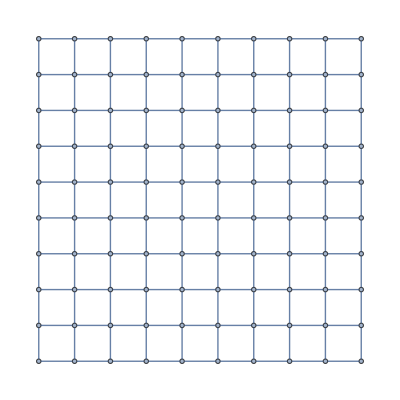

```mathematica
graph=GridGraph[{10,10}]
```

The transportation costs are uniform. Every edge is weighted 1.

```mathematica
SparseArray[{},{10,10},1]
```

SparseArray[…]

```mathematica
transportCosts=SparseArray[{},{10,10},1]
```

SparseArray[…]

```mathematica
objective = Inactive[Plus][Total[Inactive[Times][transportCosts,d],2]]
```

Inactive[Plus][Total[SparseArray[…]×d,2]]

```mathematica
Activate[objective]
```

100 d

```mathematica
objective
```

Inactive[Plus][Total[SparseArray[…]×d,2]]

```mathematica
res=SecondOrderConeOptimization[objective,{demandConstraint,
supplyConstraint,positionConstraint,0\[VectorLessEqual]y\[VectorLessEqual]1,x\[VectorGreaterEqual]0,d\[VectorGreaterEqual]0},vars];
```

The demand is also 1 for every node

```mathematica
VertexCount[graph]
```

100

```mathematica
groceryStoreCustomersDemand=SparseArray[{},100,1]
```

SparseArray[…]

```mathematica
demandConstraint=Total[x,{2}]==groceryStoreCustomersDemand;
```

```mathematica
vars=Flatten[{x∈Matrices[{5,5},Integers],y∈Vectors[5,Integers],d∈Matrices[{5,5}],Table[q[i]∈Vectors[2],{i,5}]}];
```

```mathematica
res=SecondOrderConeOptimization[objective,{demandConstraint,0\[VectorLessEqual]y\[VectorLessEqual]1,x\[VectorGreaterEqual]0,d\[VectorGreaterEqual]0},vars];
```

SecondOrderConeOptimization::scobj: The objective function … should be scalar valued.